# Hexagon at Tree Level and Integrability

## Integrand

```mathematica
Γ=Gamma;
```

```mathematica
h[a_][u_]=(u^2+a^2/4)/g^2;
μ[a_][u_]=(-1)^a g^2(Γ[a/2+I u]Γ[a/2-I u])/((a^2/4+u^2)Γ[a]);
```

## Doing the sum over Bound-states

Here we use t=τ-ⅈϕ

```mathematica
sum=FullSimplify[#,t>0]&@∑_(a=1)^∞ (h[a][u] μ[a][u] Exp[-t a+2 ⅈ u σ])/(2 π)
```

-(2 ⅇ^(-t+2 ⅈ u σ) Csch[2 π u] Sinh[2 u ArcSec[2 ⅇ^t]])/(√(4-ⅇ^(-2 t)))

## Doing the OPE integral

```mathematica
(* Integrate[sum,{u,-∞,∞}] *)
```

```mathematica
(* Integrate[sum,{u,-∞,∞},GenerateConditions->False] *)
```

```mathematica
sum/.{t->Log[Zeta[7]],σ->Zeta[5]};
ft=Integrate[%,{u,-∞,∞}]/.{Zeta[7]->Exp[t],Zeta[5]->σ}
```

1/(-1-2 ⅇ^t Cosh[σ])

```mathematica
ftOther=sum/(2π U)/.u->1/(2π)Log[U]//TrigToExp//Integrate[#,{U,0,∞},GenerateConditions->False]&//TrigToExp//FullSimplify
```

-ⅇ^σ/(ⅇ^t+ⅇ^σ+ⅇ^(t+2 σ))

```mathematica
ftOther==ft//Simplify
```

True

```mathematica
NIntegrate[sum/.{σ->1/7,t->Log[1/9]},{u,-∞,∞},WorkingPrecision->30]//Chop
ft/.{σ->1/7,t->Log[1/9]}//N[#,30]&
%/%%
```

-0.816664092908008251690110573292

-0.816664092908008251690110573292

1.

## Check against Data

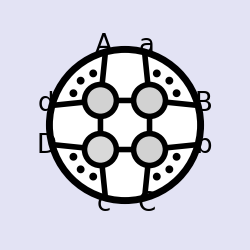
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
<<(NotebookDirectory[]<>"loop_amplitudes.m")
```

```mathematica
Zs={{√F S,0,1/(√F T),T/(√F)},{1,0,0,0},{-1,0,0,1},{0,1,-1,1},{0,1,0,0},{0,(√F)/S,1/(√F T),0}};
```

```mathematica
experiment=-evaluate@superComponent[{1,2,3,4},{},{},{},{},{}]@treeAmp[6,1]
```

(F^2 T^4)/((-1-T^2) (-1-F S T-T^2))-(F S^2 T)/(-F S^2 T-S T^2)-(F S T^3)/((1+F S T+T^2) (F S^2 T+S T^2) (-F T-F S^2 T-S T^2-F^2 S T^2-F T^3))

```mathematica
Series[experiment,{T,0,5}]//Collect[#,{T,F},Simplify]&
```

1-(S T)/(F (1+S^2))+(S^2/(F^2 (1+S^2)^2)-(2+S^2)/((1+S^2)^2)) T^2+(-S^3/(F^3 (1+S^2)^3)+(S (3+S^2))/(F (1+S^2)^3)+(F S (3+3 S^2+S^4))/((1+S^2)^3)) T^3+(3/((1+S^2)^4)+F^2/((1+S^2)^4)+S^4/(F^4 (1+S^2)^4)-(S^2 (4+S^2))/(F^2 (1+S^2)^4)) T^4+(-(6 S)/(F (1+S^2)^5)-(F^3 S)/((1+S^2)^5)-S^5/(F^5 (1+S^2)^5)+(S^3 (5+S^2))/(F^3 (1+S^2)^5)-(F S (8+10 S^2+10 S^4+5 S^6+S^8))/((1+S^2)^5)) T^5

```mathematica
resultExperiment=experiment-1/.{T->α T,F->α F}/.{T->F Exp[-t],S->Exp[σ]}//Series[#,{α,0,0}]&//Normal
```

-ⅇ^σ/(ⅇ^t+ⅇ^σ+ⅇ^(t+2 σ))

```mathematica
resultExperiment==ft//Simplify
```

True

## For Thursday’s exercise

```mathematica
Zs={{Sqrt[F1]S1,0,1/(Sqrt[F1]T1),T1/Sqrt[F1]},{1,0,0,0},{-S2/Sqrt[F2],0,0,S2/Sqrt[F2]},{-S2/Sqrt[F2],Sqrt[F2]/T2,-Sqrt[F2]/T2,S2/Sqrt[F2]+Sqrt[F2]/T2+Sqrt[F2] T2},{0,1/(Sqrt[F2]S2)+Sqrt[F2]/T2,-Sqrt[F2]/T2,Sqrt[F2]/T2},{0,1,0,0},{0,Sqrt[F1]/S1,1/(Sqrt[F1]T1),0}};
```

```mathematica
component=superComponent[{1,2,3,4},{},{},{},{},{},{}]@ratioIntegral[7,1];
```

```mathematica
experiment1Loop=component//evaluate
```

(5 F1 π^2 S1^2 T1)/(6 (-F1 S1^2 T1-S1 T1^2))+«119»+(«1»)/(«1»)-(«1»)/((F1 F2 S1^2 T1+F1 S1^2 S2 T1 T2+S1 S2 T1^2 T2+F1 F2 S1^2 T1 T2^2) «1» («1»+S1 «1»))

```mathematica
experiment1Loop/.{S1->1/2,S2->1/2,T1->1/2,T2->1/2,F1->1/2,F2->1/2}//N
```

-1.31742

```mathematica
experiment1Loop
```

(5 F1 π^2 S1^2 T1)/(6 (-F1 S1^2 T1-S1 T1^2))+«119»+(«1»)/(«1»)-(«1»)/((F1 F2 S1^2 T1+F1 S1^2 S2 T1 T2+S1 S2 T1^2 T2+F1 F2 S1^2 T1 T2^2) «1» («1»+S1 «1»))